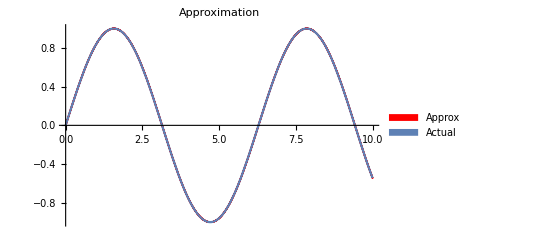

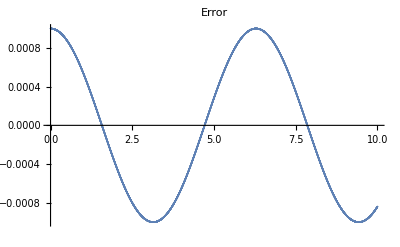

```mathematica
l=1000000;
f[t_,y_]:=l*(-y+Sin[t]);
yr[t_]:=(l*Exp[-l*t]+l^2*Sin[t]-l*Cos[t])/(1+l^2);

T=10;
t0=0;
y0=0;
h=10^(-3);

n=T/h;
y=Table[0,n+1];
y[[1]]=y0;

For[k=1,k≤n,k++,
y[[k+1]]=u/.FindRoot[u-y[[k]]==h*f[t0+(k-1)*h,u],{u,y[[k]]}];
]

myApprox=ListPlot[Table[{(k-1)*h,y[[k]]},{k,1,n+1}],PlotStyle->Red,PlotLegends->SwatchLegend[{"Approx"}],PlotLabel->Style["Approximation",24]];
realSol=Plot[yr[t],{t,0,10},PlotLegends->SwatchLegend[{"Actual"}]];
Show[myApprox,realSol]
ListPlot[Table[{(k-1)*h,yr[(k-1)*h]-y[[k]]},{k,1,n+1}],PlotLabel->Style["Error",24]]
```